```mathematica
transmission=Table[Import["/home/shardulmukim/PhD/fwi/MoS2/Longitudional/condAvg/M_10/avgCond_M10_d64_m256_c.0"<>ToString[x]<>"_p5000_rt9.dat"],{x,Range[10,80,10]}]
```

{{{-15.5,0.},{-15.4957999999999991,0.},{-15.4916,0.},{-15.4873999999999992,0.},{-15.4832000000000001,0.},4991,{5.48740000000000006,-0.013487889222222221},{5.49160000000000004,-0.013487889222222221},{5.49580000000000002,-0.013487889222222221},{5.5,-0.013487889222222221}},6,{{-15.5,0.},4998,{1}}}
 |  |  |  |

```mathematica
Dimensions[transmission]
```

{8,5000,2}

```mathematica
transmission[[5]][[5000]]
```

{5.5,-0.000761201713888888846}

```mathematica
Range[-15.5,5.5,0.00420]//Dimensions
```

{5001}

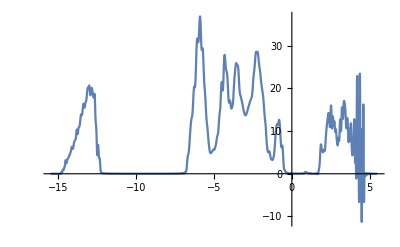

```mathematica
transmission[[5]]//ListLinePlot
```

```mathematica
Clear[data]
```

```mathematica
Clear[trainingset]
```

```mathematica
trainingset[ω_]:=Table[10*n->transmission[[n]][[ω*1000,2]],{n,Range[1,8,1]}]
```

```mathematica
trainingset[2.5]
```

{10→20.4188735333333327,20→12.6720287888888912,30→8.13426848111111234,40→5.8599451222222223,50→5.62749948311111137,60→4.23349460000000022,70→3.89477383333333327,80→3.60578773444444423}

```mathematica
Clear[data]
```

```mathematica
data[x_,ω_]:=Module[{P},P=Predict[trainingset[ω],Method->"LinearRegression"];P[x]]
```

```mathematica
data[50,4.3]
```

12.2061

```mathematica
Table[data[50,ω],{ω,Range[0.01,1,0.001]}]
```

{-0.00336032,-0.00336032,-0.00336032,-0.00336032,-0.000230499,-0.00336032,-0.00336032,-0.00336032,-0.00336032,-0.00336032,-0.00336032,-0.000230499,-0.00336032,-0.00336032,-0.00336032,-0.000230499,-0.000992846,-0.0000820891,0.0022835,0.00262307,0.0000614488,-0.00126701,0.00074398,0.00334329,0.00306736,0.000317263,-0.000954567,0.000884542,0.00498364,0.00273535,0.00142352,-0.00141218,-0.0014493,0.0038738,0.00392278,0.00349354,0.000311448,-0.00199755,-0.00132853,0.00295675,0.00828761,0.00400945,0.00069318,-0.000651607,0.000716269,0.00144057,0.00640047,0.00291213,0.00240763,-0.000831903,-0.00185858,0.00344045,0.00874163,0.00889277,0.00446308,0.00177983,-0.00115456,-0.00360072,0.00489625,0.00393336,0.00818508,0.00642653,0.0026528,-0.000582689,-0.00154957,0.000624625,0.00992871,0.00758827,0.00809468,0.00469091,0.000977262,-0.000955887,-0.000179556,-0.000886644,0.00671898,0.00847268,0.00785753,0.00489263,0.00104365,-0.00122429,-0.00050067,0.00301679,0.00695203,0.0101524,0.00969623,0.00664115,0.00236776,-0.000981664,-0.00119568,0.00129163,0.00509469,0.00939484,0.0144471,0.00956869,0.00501614,0.00104779,-0.000650927,-0.0000470257,0.00800817,0.00768139,0.0119246,0.00591084,0.00983535,0.00575956,0.00144812,-0.00197804,-0.00119343,0.00518017,0.00719908,0.015395,0.0122094,0.00766217,0.0057173,0.00290358,-0.000517045,-0.000300046,0.00751825,0.0126652,0.0158436,0.0157414,0.0121853,0.00713378,0.0022806,-0.000418576,-0.000195954,0.00643016,0.0196619,0.00740669,0.0014092,0.0129552,0.00891751,0.00504817,0.00233634,-0.000345587,0.000927836,0.000357645,0.0163384,0.0264802,0.0224292,0.0205582,0.017877,0.0116486,0.00493402,0.00044703,0.0004962,0.00671069,0.0343605,0.00103982,-0.0149337,0.00134554,-0.0290173,-0.0142662,0.00862609,0.0102009,0.0567543,0.0978136,0.188596,0.250072,0.30383,0.336936,0.378833,0.359715,0.418272,0.359569,0.315625,0.26035,0.202478,0.196019,0.228238,0.270204,0.302763,0.455245,0.539196,0.693373,0.76117,0.835701,0.773562,0.866521,0.845808,0.784646,0.806651,0.898737,0.773678,0.906887,0.863862,0.979751,0.873532,0.909956,1.03178,0.904129,0.934403,0.954399,0.863924,0.869799,0.894267,0.943986,1.09016,1.0729,1.17969,1.33846,1.38288,1.49291,1.54562,1.43468,1.62306,1.55315,1.47083,1.65043,1.51567,1.63167,1.56589,1.81582,1.98815,2.04132,2.17398,2.4743,2.79158,2.74245,2.79415,3.11119,3.03006,3.04118,3.0688,2.99898,3.04365,2.99062,2.93214,2.83798,2.8191,2.58243,2.46561,2.44278,2.29937,2.33993,2.28386,2.42419,2.11395,2.45187,2.27898,2.43156,2.67704,2.75367,2.68769,2.95906,3.03028,3.02494,3.07877,3.20169,3.15067,3.00628,3.1325,3.30646,3.0932,3.31275,3.49664,3.28815,3.48007,3.55862,3.54929,3.70635,3.43492,3.42513,3.39209,3.5017,3.57232,3.3439,3.71128,3.52651,3.68892,3.74771,3.78427,3.96466,3.93978,3.96661,3.9989,4.20314,4.17987,4.15387,4.15703,4.15886,4.41615,4.45375,4.3509,4.44449,4.23931,4.36961,4.42711,4.25856,4.10299,4.79974,4.59833,4.7325,4.58076,4.79879,4.84396,4.73784,4.74024,4.89697,4.95615,5.02457,4.99554,5.10463,5.00199,5.16269,5.10324,5.10068,5.48857,5.58274,5.84493,5.83478,5.63502,5.89968,6.14394,5.61221,6.09799,6.34566,5.89438,5.96896,6.19957,5.84114,5.97629,5.93448,6.04514,6.02007,6.06348,5.62319,5.63576,5.78622,5.81524,5.79281,5.50149,5.8442,5.85321,5.83681,5.67533,5.64818,5.62864,5.84233,5.6713,6.06135,5.96499,5.96905,5.90823,5.95926,6.28103,6.31252,6.61173,6.90446,6.62482,6.82074,6.67023,7.20256,7.38152,7.66969,7.03463,7.04215,7.32509,7.4344,7.55173,7.43142,7.20612,7.30092,8.10758,7.25043,7.00166,7.444,7.81682,7.50084,7.94386,7.26858,7.52275,7.70829,7.43177,7.05584,7.71294,7.98813,8.42558,8.2198,8.46309,8.60583,8.40572,8.94823,8.68304,9.05953,8.99483,9.27201,9.93375,9.6359,9.99307,10.0632,9.81819,10.1105,9.99578,10.3112,10.2547,9.7765,10.1868,9.93258,9.51538,9.30666,9.7574,9.28815,9.62986,9.58756,9.36424,8.76338,9.38642,9.31233,9.13904,9.73075,9.76894,9.88389,9.88515,10.3358,10.154,10.3428,10.4101,9.89122,10.3678,10.542,10.5457,10.5197,11.0732,10.5593,10.3383,10.8169,10.9516,10.6051,10.7944,11.0974,10.8446,10.8925,11.0919,10.6976,10.8853,10.9626,11.0595,11.3958,11.6341,11.3717,11.6301,11.4364,11.9059,11.7776,12.0219,12.2684,12.7761,12.6877,12.9199,12.9809,13.1578,13.3241,13.4028,13.3686,13.3867,13.7265,13.3104,13.5708,13.6205,13.372,13.5984,13.6022,13.6159,13.6029,13.4793,13.5431,13.6097,13.3059,13.4475,13.8682,13.5558,13.2475,13.649,13.5765,13.5956,13.7826,13.7945,13.7034,14.1745,14.236,14.4139,14.5625,14.8325,14.7497,14.7766,15.4214,15.4931,15.4436,15.5197,15.7141,16.0673,16.151,16.0392,16.1491,15.8771,16.3841,16.6165,15.7879,16.2304,16.6262,16.184,16.0666,15.7446,16.0092,15.822,16.1685,15.8017,15.6635,15.7016,15.5399,15.5014,15.1657,15.3251,14.9932,15.7374,15.699,15.6148,15.8519,15.8517,16.0552,16.2443,16.1378,16.2655,16.4975,16.5752,16.6817,16.5868,16.8149,16.4522,16.2817,16.1309,16.5188,16.9052,16.6732,17.0754,16.9598,16.9949,17.4788,17.3052,17.2734,17.0045,17.3411,17.8458,17.6871,17.7257,17.7072,18.2118,18.2726,18.6937,18.8344,19.1426,19.0878,19.5513,19.4283,19.8125,19.7721,19.8999,20.142,20.1931,19.8621,20.2367,19.8989,20.3785,19.8704,19.8117,20.0064,20.3137,20.0786,20.1954,20.1045,20.0592,20.091,19.9751,19.8997,19.9394,20.4169,19.898,20.5567,20.5824,19.9246,20.3407,20.3436,20.6202,20.3934,20.3612,20.3449,20.4474,20.2731,19.9242,19.7474,19.4287,19.449,19.0768,19.0469,18.4922,18.5404,18.4276,18.629,18.1198,18.3373,18.3353,17.8994,17.9134,18.097,18.2855,18.4102,18.4832,18.3509,19.1388,19.1312,19.4665,19.8158,19.552,19.8132,19.388,19.6415,19.9712,20.1765,19.84,20.1893,19.9956,20.1562,19.8946,19.6679,19.9582,19.9099,19.3186,19.5585,19.4906,19.5643,19.3514,19.7727,18.6751,19.2083,18.9477,18.798,18.7009,18.3357,18.6003,18.7026,18.4475,17.8859,18.2409,17.8461,17.7855,17.6781,17.6232,17.8568,17.2233,17.7998,17.9516,17.8312,17.2989,17.6724,18.3668,17.7147,17.5076,18.2518,18.0371,18.0394,18.4231,18.0662,18.6828,18.594,18.8161,18.4494,18.3116,17.8801,17.9317,17.1818,16.6417,16.2222,15.8495,15.0753,14.3032,14.3008,13.5336,13.3644,13.156,12.6072,12.4301,11.928,11.9569,12.1324,11.5993,11.2919,11.5181,11.3879,11.3495,10.6329,10.8199,10.3458,10.1528,9.8803,9.21666,8.70237,8.12692,7.63433,7.05317,6.54415,5.98316,5.5542,5.12208,4.8053,4.72436,4.45562,4.34041,4.31516,4.45124,4.94785,5.12176,5.38326,5.7023,5.96586,6.15825,6.46873,6.63971,6.73792,6.69307,6.64985,6.57856,6.36719,6.24439,5.95115,5.76464,5.44606,5.0964,4.87036,4.60125,4.45688,4.27945,3.99684,3.85586,3.79458,3.76551,3.6589,3.65085,3.64586,3.65411,3.63369,3.65928,3.62831,3.593,3.51974,3.43695,3.28813,3.16953,3.01407,2.79884,2.51595,2.37099,2.16048,1.87337,1.57187,1.37678,1.21689,0.969327,0.854946,0.662634,0.542889,0.455849,0.359095,0.322351,0.286877,0.213499,0.244239,0.144743,0.228529,0.242081,0.221249,0.178291,0.219179,0.216171,0.171403,0.200123,0.202254,0.187239,0.184078,0.163744,0.149713,0.139237,0.144488,0.134451,0.138726,0.126119,0.129925,0.123889,0.124828,0.131247,0.133305,0.147965,0.137873,0.116645,0.127001,0.14017,0.119639,0.132806,0.128019,0.123106,0.116564,0.110572,0.112142,0.109789,0.108263,0.100209,0.10651,0.105763,0.105072,0.105556,0.0734375,0.0953984,0.100162,0.100797,0.0913804,0.0944805,0.0861135,0.0829223,0.0711447,0.0722272,0.064087,0.0628225,0.0684462,0.0752755,0.0696641,0.0733226,0.0714869,0.0775389,0.0751455,0.0813373,0.0756879,0.0798541,0.0734075,0.0622138,0.0726403,0.0772863,0.067722,0.0731,0.0550289,0.0682922,0.0649414,0.0535006,0.0559638,0.0610044,0.055812,0.0604524,0.0563214,0.0587751,0.0601384,0.0642745,0.0630929,0.0646461,0.0578521,0.0644457,0.0711275,0.0601801,0.0663873,0.0643195,0.0509728,0.057114,0.050029,0.0557027,0.0533786,0.0375362,0.0410849,0.0335712,0.043097,0.0419141,0.0444337,0.0446465,0.0431713,0.0440227,0.0464866,0.0484214,0.0499649,0.0498415,0.0531096,0.0475363,0.0442547,0.037686,0.044596,0.0522654,0.0478284,0.0403792,0.0304143,0.0402421,0.0419738,0.0391067,0.0328278,0.0277874,0.0313595,0.0367913,0.036617,0.0381136,0.0393741,0.0409627,0.0428438,0.0431338,0.046583,0.046981,0.0479674,0.0490884,0.0496599,0.0473539,0.045969,0.0388481,0.0378932,0.0404983,0.0291503,0.0271676,0.0299137,0.0303046,0.027609,0.0279043,0.0277317,0.0295142,0.0275632,0.0326659,0.0317306,0.032176,0.0368145,0.036855,0.0395572,0.0394287,0.0376178,0.0402536,0.0398196,0.0390251,0.034548,0.0364938,0.0308677,0.0312462,0.0307229,0.0292271,0.0226571,0.0237426,0.0207253,0.0267567,0.0263937,0.0271893,0.0279324,0.0321354,0.0310971,0.0326323,0.0322305,0.0331824,0.0364012,0.0367297,0.037309,0.0368597,0.0321455,0.0307142,0.0284122,0.0254233,0.0282512,0.0240234,0.0266897,0.0175879,0.0233817,0.021898,0.0227465,0.0200515,0.0229157,0.0196274,0.0227818,0.0237869,0.0257681,0.0257383,0.0274443,0.0300827,0.030997,0.031847,0.0321559,0.0335836,0.0337754,0.0314987,0.0278441,0.0285658,0.0255118,0.0225857,0.0240724,0.0219093,0.0216739,0.020089,0.0204296,0.0154879,0.0200107,0.0211634,0.0205938,0.0235197,0.0259662,0.0250084}

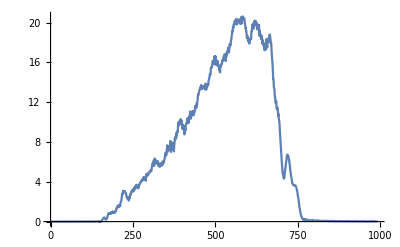

```mathematica
ListPlot[%13,Joined->True]
```

```mathematica
ParallelTable[{x,data[x,1]},{x,Range[1,80,1]}]
```

{{1,{14.968,15.0217,14.9142}},{2,{14.979,15.0327,14.9253}},{3,{14.99,15.0437,14.9363}},{4,{15.0011,15.0548,14.9474}},{5,{15.0121,15.0658,14.9584}},{6,{15.0178,15.0714,14.9642}},{7,{15.0342,15.0879,14.9805}},{8,{15.0453,15.099,14.9916}},{9,{15.0563,15.11,15.0026}},{10,{15.0673,15.1211,15.0136}},{11,{15.0742,15.1278,15.0206}},{12,{15.0894,15.1431,15.0357}},{13,{15.1005,15.1542,15.0468}},{14,{15.1115,15.1652,15.0578}},{15,{15.1226,15.1763,15.0689}},{16,{15.1336,15.1873,15.0799}},{17,{15.1447,15.1984,15.0909}},{18,{15.1557,15.2094,15.102}},{19,{15.1635,15.2171,15.1099}},{20,{15.1747,15.2283,15.1211}},{21,{15.1888,15.2425,15.1351}},{22,{15.1999,15.2536,15.1462}},{23,{15.2109,15.2646,15.1572}},{24,{15.222,15.2757,15.1683}},{25,{15.233,15.2867,15.1793}},{26,{15.2414,15.295,15.1878}},{27,{15.2551,15.3088,15.2014}},{28,{15.2661,15.3198,15.2124}},{29,{15.2772,15.3309,15.2235}},{30,{15.2882,15.3419,15.2345}},{31,{15.2975,15.3511,15.2439}},{32,{15.3103,15.364,15.2566}},{33,{15.3199,15.3734,15.2663}},{34,{15.331,15.3846,15.2774}},{35,{15.3434,15.3971,15.2897}},{36,{15.3532,15.4068,15.2997}},{37,{15.3644,15.418,15.3108}},{38,{15.3766,15.4303,15.3229}},{39,{15.3876,15.4413,15.3339}},{40,{15.3987,15.4524,15.345}},{41,{15.4097,15.4634,15.356}},{42,{15.4207,15.4745,15.367}},{43,{15.4318,15.4855,15.3781}},{44,{15.4428,15.4965,15.3891}},{45,{15.4539,15.5076,15.4002}},{46,{15.4649,15.5186,15.4112}},{47,{15.476,15.5297,15.4223}},{48,{15.487,15.5407,15.4333}},{49,{15.4985,15.5521,15.445}},{50,{15.5091,15.5628,15.4554}},{51,{15.5201,15.5738,15.4664}},{52,{15.5312,15.5849,15.4775}},{53,{15.5422,15.5959,15.4885}},{54,{15.5545,15.6081,15.5009}},{55,{15.5643,15.618,15.5106}},{56,{15.5754,15.6291,15.5217}},{57,{15.5864,15.6401,15.5327}},{58,{15.5992,15.6528,15.5457}},{59,{15.6085,15.6622,15.5548}},{60,{15.6216,15.6752,15.568}},{61,{15.6326,15.6861,15.579}},{62,{15.6416,15.6953,15.5879}},{63,{15.6527,15.7064,15.599}},{64,{15.6637,15.7174,15.61}},{65,{15.6748,15.7285,15.621}},{66,{15.6858,15.7395,15.6321}},{67,{15.6968,15.7506,15.6431}},{68,{15.7107,15.7643,15.6572}},{69,{15.7189,15.7726,15.6652}},{70,{15.73,15.7837,15.6763}},{71,{15.741,15.7947,15.6873}},{72,{15.7521,15.8058,15.6984}},{73,{15.7631,15.8168,15.7094}},{74,{15.7782,15.8317,15.7246}},{75,{15.7852,15.8389,15.7315}},{76,{15.7962,15.8499,15.7425}},{77,{15.8073,15.861,15.7536}},{78,{15.8229,15.8765,15.7693}},{79,{15.8294,15.8831,15.7757}},{80,{15.8404,15.8941,15.7867}}}

```mathematica
LaunchKernels[4]
```

SubKernels`SubKernels::timekernels: Timeout for subkernels. Received only 0 of 4 connections.

{}

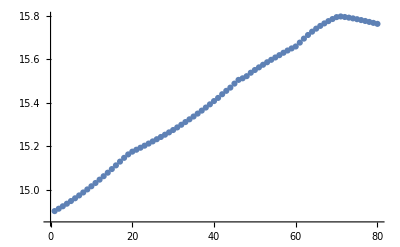

```mathematica
ListPlot[%8]
```

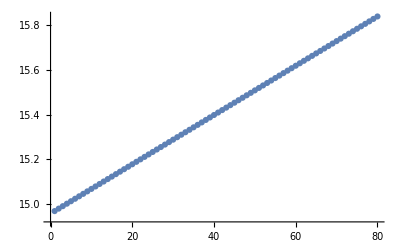

```mathematica
ListPlot[%5]
```

```mathematica
Range[0.001,5,0.001]//Dimensions
```

{5000}

```mathematica
Table[data[5,ω],{ω,Range[0.001,5,0.001]}]
```

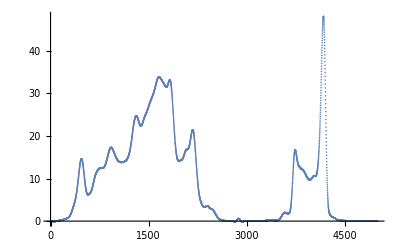

```mathematica
ListPlot[%37]
```

```mathematica
Table[Export["/home/shardulmukim/PhD/fwi/MoS2/Longitudional/condAvg/data_"<>ToString[y]<>"_.dat",ParallelTable[data[y,x],{x,Range[0.001,5,0.001]}]],{y,Range[80,150,5]}]
```

```mathematica
Dimensions[%49]
```

{15,301}

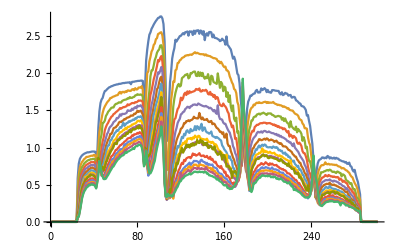

```mathematica
ListLinePlot[Table[%49[[x]],{x,15}]]
```

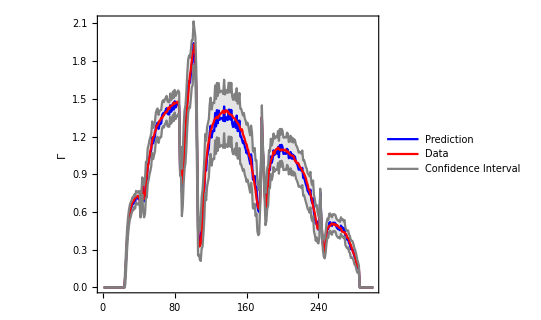

```mathematica
Show[ListLinePlot[{Transpose[%4][[3]],Transpose[Import["/home/shardul/fwi/AGNR/7AGNR/100unitcells/resolve/test31.dat"]][[2]],Transpose[%4][[1]],Transpose[%4][[2]]},PlotStyle->{Blue,Red,Gray,Gray},Filling->{3->{4}},PlotLegends->Placed[{"Prediction","Data","Confidence Interval"},{Right,Top}],AspectRatio->0.7],FrameLabel->{{HoldForm[Γ],None},{None,None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0.1]},Frame->True]
```

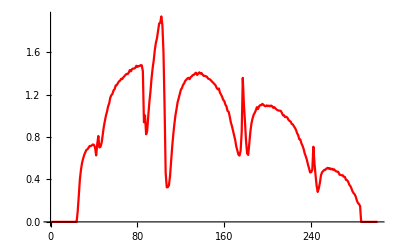

```mathematica
ListLinePlot[Transpose[Import["/home/shardul/fwi/AGNR/7AGNR/100unitcells/resolve/test31.dat"]][[2]],PlotStyle->Red]
```

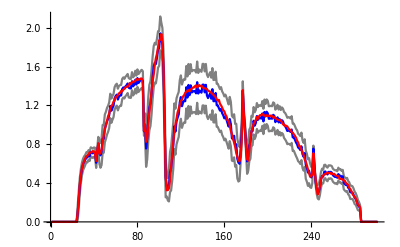

```mathematica
Show[%5,%6]
```

```mathematica
Show[%107,%108]
```

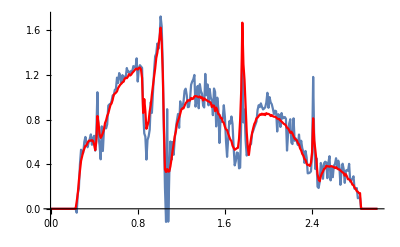

-Graphics-

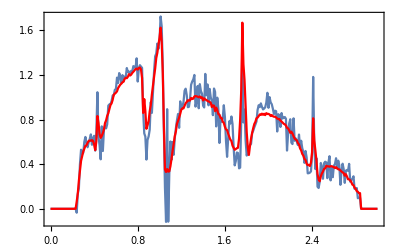

```mathematica
Show[%24,Frame->True]
```

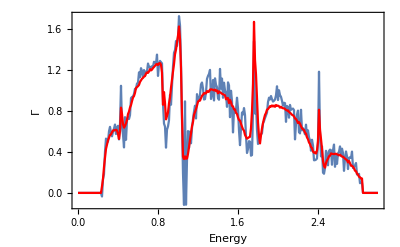

```mathematica
Show[%25,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Energy],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

```mathematica
Table[p[x],{x,5,35,5}]
```

{2.62554,2.50093,2.37632,2.2517,2.12709,2.00248,1.87786}

```mathematica
Table[p[]]
```

PredictorFunction[…]

```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
Clear[LEFT]
```

```mathematica
Lead=Table[ToExpression[Import["/home/shardul/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{{1},299,{{0.461335-0.0000344515 ⅈ,0.191132-0.0000279943 ⅈ,0.112061-0.0000304181 ⅈ,0.048645-0.0000174145 ⅈ,7,0.0964055-0.0000346394 ⅈ,0.117282-0.0000339417 ⅈ,0.192872-0.0000292268 ⅈ},{1},10,{1},{1}}}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Lead[[ω*100+1]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:=Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
tr[0.7,0.0001,1,0]
```

2.

```mathematica
pris:=pris= Table[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,3,0.01]}]
```

```mathematica
ListLinePlot[ParallelTable[{ω,tr[ω,0.0001,1,0]},{ω,Range[00,3,0.01]}]]
```

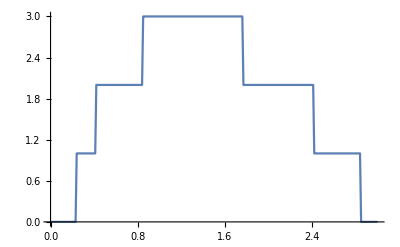

```mathematica
RandomInteger[{1,14}]
```

```mathematica
imp[ω_,ϵ1_]:=Module[{μ=RandomInteger[{1,14}]},Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ,μ}}->ω+ⅈ*0.0001-ϵ1]]]]
```

```mathematica
RandomSample[Join[Table[imp[ω,0.5],40],Table[imp[ω,0],60]]]
```

```mathematica
data:=Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{},lista={RandomSample[Join[Table[imp[ω,0.5],40],Table[imp[ω,0],60]]]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
m5=ParallelTable[{ω,tra},{ω,Range[0,3,0.01]}];
m5]
```

```mathematica
Table[data,100]
```

{1}
 |  |  |  |

```mathematica
υ=Module[{},ρ1:= Table[Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]-transmission100[[ξ]][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{ξ,95}]; 
{ρ1}];
υ
```